## Problem 7.5

```mathematica
ps=n*e0*c*E0^2*1/(2*Pi)*Integrate[Exp[I*t*(w-w0)],{t,-T/2,T/2}]
```

(c e0 E0^2 n Sin[1/2 T (w-w0)])/(π (w-w0))

```mathematica
c=3*10^8;
e0=8.85*10^-12;
E0=1;
n=1;
```

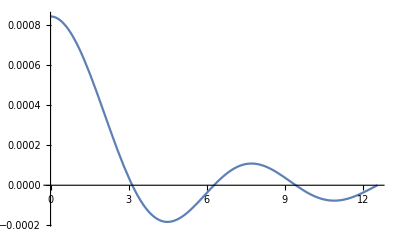

```mathematica
Plot[c e0 E0^2 n/Pi*Sinc[deltaw],{deltaw,0,4*Pi}]
```